## Sept 14: Test Problem for Trust-Region Sub-Problem Interaction with Julia trs package and Dan’s code

There are two bits we need to test.

```mathematica
Clear[p,q]
n=6;
Hk = RandomReal[{-1,1},{n,n}]; Hk = Hk+Hkᵀ;
Delf= RandomReal[{-1,1},n];
Rad=0.5;
InvHk =  Inverse[Hk];
m1[p_] := 0.5 p.InvHk.p + Delf.p
m[q_]:= 0.5 q.Hk.q + (Hk.Delf).q
{p0,q0}=RandomReal[{-1,1},{2,n}];
{pval, psub}= FindMinimum[ {m1[p], p.p≤ Rad^2},{p,p0}];
pStar=p/.psub;
{qval, qsub}= FindMinimum[ {m[q], (Hk.q).(Hk.q)≤ Rad^2},{q,q0}];
qStar=q/.qsub;
{pval-qval,Norm[pStar-Hk.qStar], Norm[pStar]-Rad, Norm[Hk.qStar]-Rad}
```

{-1.33227×10^-15,6.21551×10^-12,-4.88288×10^-8,-4.88288×10^-8}

```mathematica
{u1,u2} = Orthogonalize[ RandomReal[{-1,1},{2,n}]];
ϵ=0.1;
Data = Table[
q=Rad*Normalize[ pStar+ ϵ z1 u1 +ϵ z2 u2];
 m[q],
{z1,-1,1,0.1},{z2,-1,1,0.1}];
ListContourPlot[Data,
DataRange->{{-ϵ,ϵ},{-ϵ,ϵ}},
Contours->30,
PlotLabel->{val,Norm[pStar]-Rad,"Checking for On the Boundary"},
Epilog->{Red, Point[{0,0}]}];
```

## before Sept 14

```mathematica
(* V = A.U and all are "H" updates.  All need symm  Uᵀ.V = Vᵀ.U  *)
SR1[H_,{U_,V_}]:= Module[{δ=10^-5,T},
T=PseudoInverse[(U-H.V)ᵀ.V,Tolerance->δ];
(*Print["SR1",Eigenvalues[T]];*)
H+(U-H.V).T.(U-H.V)ᵀ]

BFGS[H_,{U_,V_}]:= Module[
{δ=10^-5,T,Id=IdentityMatrix[Length[H]]},
T=PseudoInverse[Uᵀ.V,Tolerance->δ];
(*Print["BFGS",Eigenvalues[T]];*)
U.T.Uᵀ +(Id-U.T.Vᵀ).H.(Id-V.T.Uᵀ)]

DFP[H_,{U_,V_}]:= Module[
{δ=10^-5,HV,T1,T2},
HV = H.V;
T1=PseudoInverse[Uᵀ.V,Tolerance->δ];
T2 = PseudoInverse[Vᵀ.HV,Tolerance->δ];
(*Print["DFP",Eigenvalues[T1]];*)
H - HV.T2.HVᵀ+U.T1.Uᵀ]

PSB[H_,{U_,V_}]:= Module[
{δ=10^-5,VtVInv,VVtVInvUMinusHVt},
(* Now correct yet !!!! *)
(* There are typos in http://people.math.sfu.ca/~elushi/project_833.pdf *)
(* There are typos in Nicolas Boutet and Rob Haelterman and Joris Degroote:Ref p6 DX is S and DG is Y Formula below Formula 4 has typos! *)
(* The best ref is Robert Schnabel Quasi-Newton Methods Using Multiple Secant equations CU-CS-247-83 Eq 3.6 p19.As before DX is S and DG is Y BUT H is the approximation to A not $A^{-1}$.Since everything this is self dual I get the inverse formula by flipping DX and DG. *) 
VtVInv=PseudoInverse[Vᵀ.V, Tolerance->δ];
VVtVInvUMinusHVt =V.VtVInv.(U-H.V)ᵀ ;
(*Print["PSB",Eigenvalues[Vᵀ.V]];*)
H + VVtVInvUMinusHVtᵀ+VVtVInvUMinusHVt-VVtVInvUMinusHVt.V.VtVInv.Vᵀ
]
```

### Tracking Down PSB typos and Blocking the Updates

Non-block version.

```mathematica
{n,b}={12,2};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+ Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
s=RandomReal[{-1,1},n];
y=A.s;
H = H0 +(KroneckerProduct[s-H0.y,y]+ KroneckerProduct[y,s-H0.y])/(yᵀ.y)-(KroneckerProduct[y,s-H0.y].KroneckerProduct[y,y])/(yᵀ.y)^2;
Norm[s- H.y]
```

3.76536×10^-15

Block version using S and Y.  I am not sure whey we are using U and V in the paper but we are.

```mathematica
{n,b}={127,5};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+ Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
S=RandomReal[{-1,1},{n,b}];
Y=A.S;
δ=1.0 10^-5;
YtYInv=PseudoInverse[Yᵀ.Y, Tolerance->δ];
H =H0 + (S-H0.Y).YtYInv.Yᵀ+Y.YtYInv.(S-H0.Y)ᵀ-Y.YtYInv.(S-H0.Y)ᵀ.Y.YtYInv.Yᵀ;
Map[Norm[#,"Frobenius"]&, { H.Y-S, H-Hᵀ} ]
```

{1.19096×10^-12,1.68674×10^-14}

Block version using U and V with some common subexpression elimination.

```mathematica
{n,b}={327,12};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+ Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
U=RandomReal[{-1,1},{n,b}];
V=A.U;
δ=1.0 10^-6;
VtVInv=PseudoInverse[Vᵀ.V, Tolerance->δ];
VVtVInvUMinusHVt =V.VtVInv.(U-H0.V)ᵀ ;
H =H0 + VVtVInvUMinusHVtᵀ+VVtVInvUMinusHVt-VVtVInvUMinusHVt.V.VtVInv.Vᵀ;
Map[Norm[#,"Frobenius"]&, { H.V-U, H-Hᵀ} ]
```

{1.25459×10^-11,2.74218×10^-14}

### Testing SR1, BFGS, PSB, and DFP

First check the Secant condition and symmetry.

```mathematica
{n,b}={529,23};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+ Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
U= Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U;
H1S = SR1[H0,{U,V}];
H1B = BFGS[H0,{U,V}];
H1D = DFP[H0,{U,V}];
H1P = PSB[H0,{U,V}];
Map[ Norm[U-#.V,"Frobenius"]&,{H1S,H1B,H1D,H1P}]
Map[ Norm[#ᵀ-#,"Frobenius"]&,{H1S,H1B,H1D,H1P}]
```

{1.06195×10^-11,6.69417×10^-10,1.30387×10^-11,6.00406×10^-12}

{6.65608×10^-12,4.78378×10^-10,9.62985×10^-12,1.96793×10^-13}

## Convergence: No Orthogonalization

Next check the convergence or lack there of  with no orthogonalization

### Well conditioned SPD

| SR1 | BFGS | DFP | PSB
1 | 0.901441 | 1.02139 | 0.90146 | 0.950327
2 | 0.808016 | 1.04061 | 0.808059 | 0.907531
3 | 0.727641 | 1.05179 | 0.727708 | 0.873307
4 | 0.646819 | 1.05385 | 0.646928 | 0.843
5 | 0.564377 | 1.0545 | 0.564548 | 0.813136
6 | 0.488064 | 1.05036 | 0.488341 | 0.791275
7 | 0.415984 | 1.04168 | 0.416382 | 0.771921
8 | 0.342815 | 1.03654 | 0.343637 | 0.755474
9 | 0.28368 | 1.02321 | 0.2852 | 0.737827
10 | 0.223643 | 1.00832 | 0.227266 | 0.72606
11 | 0.167953 | 0.995196 | 0.174955 | 0.711143
12 | 0.111597 | 0.98614 | 0.127733 | 0.698957

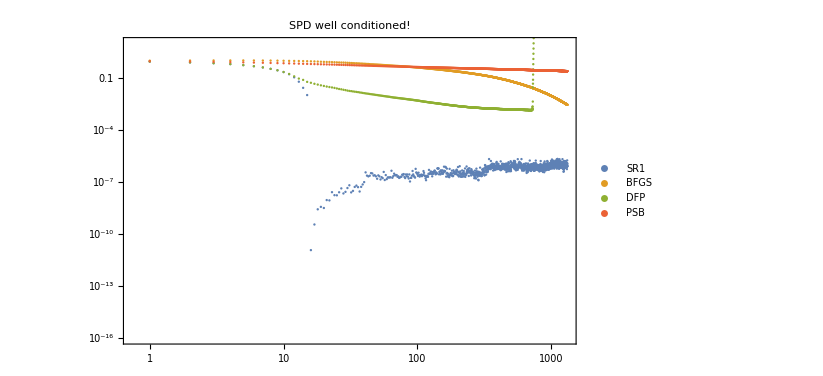

```mathematica
{n,b}={125,4};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A.Aᵀ +1.0 IdentityMatrix[n],H0.H0ᵀ};
InvA=Inverse[A];
MaxIter=1320;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
Data=Table[
U= Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-16,10},
GridLines->Automatic,
PlotLabel->"SPD well conditioned!",
Frame->True]
```

### Not so well conditioned SPD

| SR1 | BFGS | DFP | PSB
1 | 0.998786 | 0.998533 | 0.998785 | 0.999253
2 | 0.998534 | 0.99783 | 0.998533 | 0.998716
3 | 0.9983 | 0.996615 | 0.998298 | 0.998194
4 | 0.997778 | 0.996613 | 0.997776 | 0.997808
5 | 0.997249 | 0.996116 | 0.997246 | 0.997409
6 | 0.997093 | 0.995855 | 0.997089 | 0.997097
7 | 0.997182 | 0.995557 | 0.997174 | 0.996846
8 | 0.997844 | 0.995213 | 0.997825 | 0.996623
9 | 0.997764 | 0.994584 | 0.997743 | 0.996397
10 | 0.997745 | 0.994079 | 0.997708 | 0.996225
11 | 0.997885 | 0.993726 | 0.997814 | 0.99605
12 | 0.99818 | 0.993361 | 0.998068 | 0.995904

| SR1 | BFGS | DFP | PSB
1 | 1.10992×10^19 | 0.980876 | 0.99976 | 0.992851
2 | 6.59535×10^19 | 0.980875 | 0.999761 | 0.99285
3 | 3.69355×10^19 | 0.980865 | 0.999762 | 0.992849
4 | 1.96399×10^19 | 0.980853 | 0.999763 | 0.992848
5 | 4.59793×10^19 | 0.980855 | 0.999764 | 0.992847
6 | 3.50762×10^16 | 0.980851 | 0.999766 | 0.992846
7 | 4.77791×10^19 | 0.980852 | 0.999766 | 0.992844
8 | 3.26216×10^18 | 0.980868 | 0.999768 | 0.992843
9 | 6.69148×10^19 | 0.980862 | 0.999769 | 0.992842
10 | 3.61161×10^19 | 0.980852 | 0.999769 | 0.99284
11 | 9.38496×10^19 | 0.980838 | 0.99977 | 0.992839
12 | 1.09027×10^20 | 0.980838 | 0.999772 | 0.992838

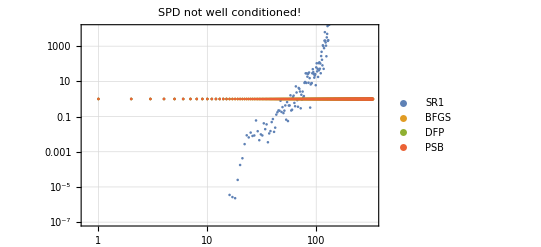

```mathematica
{n,b}={125,4};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A.Aᵀ +0.0 IdentityMatrix[n],H0.H0ᵀ};
InvA=Inverse[A];
MaxIter=332;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
Data=Table[
U= Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
TableForm[Data⟦-12;;-1⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-7,10^4},
GridLines->Automatic,
PlotLabel->"SPD not well conditioned!",
Frame->True]
```

### Symmetric but Not SPD

| SR1 | BFGS | DFP | PSB
1 | 2.77794 | 46.5141 | 2.75701 | 0.477609
2 | 0.0693614 | 884.35 | 1.23149 | 0.329519
3 | 3.02437×10^-12 | 7302.98 | 0.636157 | 0.266324
4 | 2.78586×10^-12 | 36028.3 | 0.333439 | 0.231518
5 | 6.63678×10^-12 | 900208. | 14.7633 | 0.210311
6 | 4.29525×10^-12 | 1.37499×10^7 | 0.491624 | 0.196198
7 | 4.62749×10^-12 | 4.36635×10^8 | 0.37753 | 0.187604
8 | 3.99099×10^-12 | 2.47352×10^9 | 0.37721 | 0.179962
9 | 2.91184×10^-12 | 1.97929×10^10 | 4.1548 | 0.174678
10 | 4.7547×10^-12 | 1.48176×10^13 | 0.683342 | 0.170595
11 | 6.39002×10^-12 | 1.15909×10^15 | 0.811954 | 0.167911
12 | 5.25196×10^-12 | 9.15281×10^15 | 0.196222 | 0.165442

| SR1 | BFGS | DFP | PSB
1 | 4.08201×10^-12 | 1.32705×10^182 | 1.32908×10^32 | 0.133412
2 | 4.11452×10^-12 | 3.13188×10^183 | 2.65815×10^32 | 0.133322
3 | 5.42082×10^-12 | 2.46543×10^184 | 5.3163×10^32 | 0.133246
4 | 4.45204×10^-12 | 7.06201×10^185 | 1.06326×10^33 | 0.133158
5 | 5.32653×10^-12 | 1.59219×10^187 | 2.12652×10^33 | 0.133071
6 | 5.45664×10^-12 | 2.99288×10^188 | 4.25304×10^33 | 0.133004
7 | 6.20011×10^-12 | 7.34165×10^189 | 8.50608×10^33 | 0.132938
8 | 6.61596×10^-12 | 5.84171×10^191 | 1.70122×10^34 | 0.132851
9 | 5.86156×10^-12 | 9.7566×10^192 | 3.40243×10^34 | 0.132751
10 | 4.55529×10^-12 | 1.06239×10^194 | 6.80487×10^34 | 0.132683
11 | 4.90831×10^-12 | 3.46745×10^194 | 1.36097×10^35 | 0.132586
12 | 6.5158×10^-12 | 3.31252×10^196 | 2.72195×10^35 | 0.132497

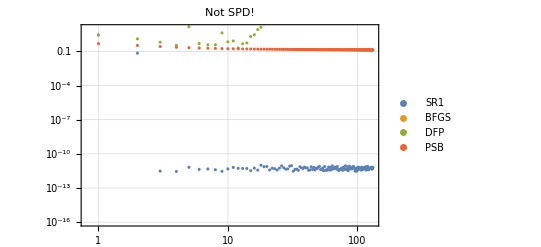

```mathematica
{n,b}={125,34};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+Aᵀ ,H0+H0ᵀ};
InvA=Inverse[A];
MaxIter=132;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
Data=Table[
U= Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
TableForm[Data⟦-12;;-1⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-16,10},
GridLines->Automatic,
PlotLabel->"Not SPD!",
Frame->True]
```

## Convergence: Orthogonalization

Next check the convergence or lack there of  with orthogonalization

### Well conditioned SPD

| SR1 | BFGS | DFP | PSB
1 | 0.876458 | 1.0361 | 0.876485 | 0.937679
2 | 0.762392 | 0.983903 | 0.76247 | 0.916331
3 | 0.656868 | 0.966979 | 0.657101 | 0.903853
4 | 0.55633 | 0.952909 | 0.557646 | 0.901402
5 | 0.464794 | 0.944596 | 0.474984 | 0.899421
6 | 0.375143 | 0.935289 | 0.42509 | 0.898613
7 | 0.291801 | 0.929027 | 0.400259 | 0.897805
8 | 0.220324 | 0.9232 | 0.387743 | 0.897367
9 | 0.154311 | 0.918155 | 0.377557 | 0.8969
10 | 0.097161 | 0.913986 | 0.369729 | 0.896596
11 | 0.0511798 | 0.90996 | 0.362382 | 0.896266
12 | 0.0596147 | 0.906687 | 0.356229 | 0.896029

| SR1 | BFGS | DFP | PSB
1 | 1.06083 | 0.816457 | 6.65175×10^110 | 0.883114
2 | 1.03309 | 0.816452 | 1.33035×10^111 | 0.883094
3 | 1.06027 | 0.816445 | 2.6607×10^111 | 0.883074
4 | 1.0326 | 0.81644 | 5.3214×10^111 | 0.883054
5 | 1.05972 | 0.816433 | 1.06428×10^112 | 0.883034
6 | 1.03212 | 0.816428 | 2.12856×10^112 | 0.883014
7 | 1.05918 | 0.816421 | 4.25712×10^112 | 0.882994
8 | 1.03167 | 0.816416 | 8.51424×10^112 | 0.882974
9 | 1.05866 | 0.81641 | 1.70285×10^113 | 0.882954
10 | 1.03124 | 0.816405 | 3.4057×10^113 | 0.882934
11 | 1.05815 | 0.816399 | 6.81139×10^113 | 0.882914
12 | 1.03084 | 0.816394 | 1.36228×10^114 | 0.882894

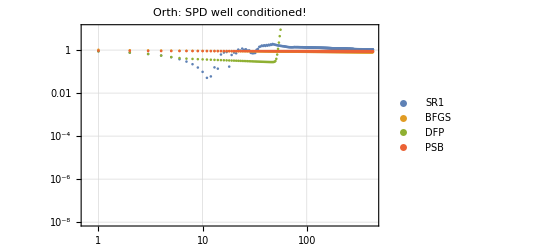

```mathematica
{n,b}={125,5};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A.Aᵀ +1.0 IdentityMatrix[n],H0.H0ᵀ};
InvA=Inverse[A];
MaxIter=432;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
U= U0=Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U0;
U2 = Orthogonalize[(V-U0.U0ᵀ.V)ᵀ]ᵀ;
Data=Table[
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
UNew = Orthogonalize[(V-U.Uᵀ.V)ᵀ]ᵀ;
(*Print[Norm[Uᵀ.UNew]];*)
U=UNew;
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
TableForm[Data⟦-12;;-1⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-8,10},
GridLines->Automatic,
PlotLabel->"Orth: SPD well conditioned!",
Frame->True]
```

### Not so well conditioned SPD

| SR1 | BFGS | DFP | PSB
1 | 0.948058 | 1.02152 | 0.948067 | 0.970004
2 | 0.893068 | 0.993384 | 0.893093 | 0.957964
3 | 0.848617 | 0.984237 | 0.848672 | 0.952406
4 | 0.807626 | 0.979133 | 0.807883 | 0.951274
5 | 0.77161 | 0.975663 | 0.772552 | 0.950467
6 | 0.741312 | 0.97212 | 0.748731 | 0.950088
7 | 0.718541 | 0.969951 | 0.740387 | 0.949768
8 | 0.698701 | 0.967809 | 0.736808 | 0.949548
9 | 0.679742 | 0.966126 | 0.733432 | 0.949365
10 | 0.666839 | 0.964653 | 0.731037 | 0.949226
11 | 0.658528 | 0.96339 | 0.728572 | 0.949104
12 | 0.654596 | 0.962275 | 0.726724 | 0.94901

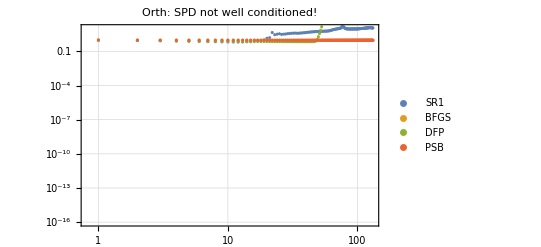

```mathematica
{n,b}={125,4};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A.Aᵀ +0.0 IdentityMatrix[n],H0.H0ᵀ};
InvA=Inverse[A];
MaxIter=132;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
U= U0=Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U0;
U2 = Orthogonalize[(V-U0.U0ᵀ.V)ᵀ]ᵀ;
Data=Table[
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
UNew = Orthogonalize[(V-U.Uᵀ.V)ᵀ]ᵀ;
(*Print[Norm[Uᵀ.UNew]];*)
U=UNew;
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-16,10},
GridLines->Automatic,
PlotLabel->"Orth: SPD not well conditioned!",
Frame->True]
```

### Not SPD

The behavior is different depending on the relative sample size!   Relatively big sample size! SR1 resolves rapidly PSB slow and steady nothing else useful.  BFGS overflows!

| SR1 | BFGS | DFP | PSB
1 | 5.01679 | 25.2895 | 5.0647 | 0.933389
2 | 3.76215 | 4127.65 | 10.9135 | 0.879624
3 | 3.07047 | 1.83954×10^6 | 17.9508 | 0.866893
4 | 3.49493 | 8.15956×10^8 | 4.11062 | 0.861325
5 | 4.36099 | 5.28743×10^14 | 4.50592 | 0.858616
6 | 4.45132 | 2.48149×10^17 | 4.8305 | 0.856661
7 | 4.05296 | 9.28978×10^19 | 7.34812 | 0.855417
8 | 28.3496 | 1.25353×10^23 | 17.0194 | 0.854439
9 | 1.92155 | 5.80387×10^25 | 107.16 | 0.853694
10 | 450.1 | 5.25561×10^28 | 17.1407 | 0.853088
11 | 1.35722 | 2.75098×10^31 | 9.27386 | 0.852574
12 | 9.42348 | 1.88978×10^34 | 7.87857 | 0.852162

| SR1 | BFGS | DFP | PSB
1 | 19.3798 | 3.03983×10^58 | 5.1548 | 0.850481
2 | 20.5817 | 1.45212×10^61 | 5.17116 | 0.850416
3 | 24.181 | 5.66989×10^63 | 5.13652 | 0.850358
4 | 26.9819 | 2.64115×10^66 | 5.15233 | 0.850311
5 | 28.6377 | 9.83844×10^68 | 5.13456 | 0.85027
6 | 32.0968 | 4.46273×10^71 | 5.14817 | 0.850236
7 | 32.4402 | 1.59603×10^74 | 5.13996 | 0.850205
8 | 35.5983 | 7.08317×10^76 | 5.15103 | 0.85018
9 | 35.4589 | 2.45662×10^79 | 5.14826 | 0.850157
10 | 37.2778 | 1.07838×10^82 | 5.15702 | 0.850138
11 | 37.5841 | 3.67573×10^84 | 5.15728 | 0.85012
12 | 37.196 | 1.61498×10^87 | 5.16412 | 0.850105

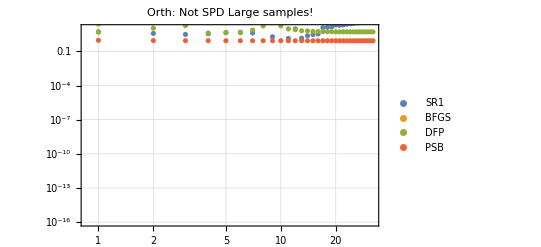

```mathematica
{n,b}={125,4};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
MaxIter=123;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
U= U0=Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U0;
U2 = Orthogonalize[(V-U0.U0ᵀ.V)ᵀ]ᵀ;
Data=Table[
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
UNew = Orthogonalize[(V-U.Uᵀ.V)ᵀ]ᵀ;
(*Print[Norm[Uᵀ.UNew]];*)
U=UNew;
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
TableForm[Data⟦-12;;-1⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-16,10},
GridLines->Automatic,
PlotLabel->"Orth: Not SPD Large samples!",
Frame->True]
```

Small sample sizes SR1 bounces PSB as always slow and steady!

| SR1 | BFGS | DFP | PSB
1 | 4.12608 | 10.1539 | 4.70871 | 0.958227
2 | 3.34751 | 4670.97 | 12.8776 | 0.919147
3 | 3.78737 | 651890. | 3.96161 | 0.907065
4 | 2.88767 | 4.088×10^8 | 10.3809 | 0.902024
5 | 7.04937 | 2.77152×10^11 | 9.92254 | 0.899307
6 | 3.54207 | 1.92812×10^15 | 7.46128 | 0.897616
7 | 22.2256 | 7.4488×10^21 | 9.77466 | 0.896595
8 | 3.05504 | 7.01109×10^25 | 9.44478 | 0.895892
9 | 21.026 | 3.2265×10^29 | 13.9378 | 0.895413
10 | 51.1856 | 1.32748×10^33 | 16.2467 | 0.89504
11 | 6.33367 | 1.36633×10^36 | 25.6615 | 0.894766
12 | 3.33658 | 4.95208×10^39 | 32.8597 | 0.894535

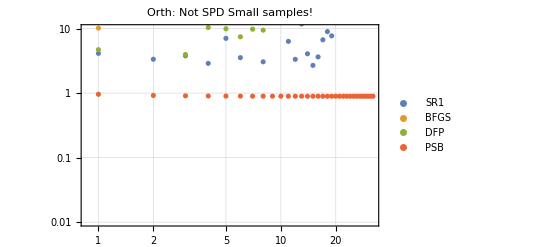

```mathematica
{n,b}={125,3};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
MaxIter=32;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
U= U0=Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U0;
U2 = Orthogonalize[(V-U0.U0ᵀ.V)ᵀ]ᵀ;
Data=Table[
V=A.U;
Hs = SR1[Hs,{U,V}];
Hb = BFGS[Hb,{U,V}];
Hd = DFP[Hd,{U,V}];
Hp = PSB[Hp,{U,V}];
UNew = Orthogonalize[(V-U.Uᵀ.V)ᵀ]ᵀ;
(*Print[Norm[Uᵀ.UNew]];*)
U=UNew;
Map[ Norm[#-InvA,"Frobenius"]&,{Hs,Hb,Hd,Hp}],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
Algs = {"SR1","BFGS","DFP","PSB"};
TableForm[Data⟦1;;12⟧,TableHeadings->{Automatic,Algs}]
ListLogLogPlot[Dataᵀ,PlotLegends->Algs,
PlotRange->{10^-2,10},
GridLines->Automatic,
PlotLabel->"Orth: Not SPD Small samples!",
Frame->True]
```

Looking at just the PSB code

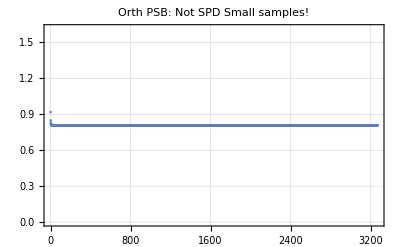

```mathematica
{n,b}={125,5};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
MaxIter=3267;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
U= U0=Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U0;
U2 = Orthogonalize[(V-U0.U0ᵀ.V)ᵀ]ᵀ;
Data=Table[
V=A.U;
Hp = PSB[Hp,{U,V}];
UNew = Orthogonalize[(V-U.Uᵀ.V)ᵀ]ᵀ;
(*Print[Norm[Uᵀ.UNew]];*)
U=UNew;
Norm[Hp-InvA,"Frobenius"],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
ListPlot[Data,
GridLines->Automatic,
PlotLabel->"Orth PSB: Not SPD Small samples!",
Frame->True]
```

PSB is slow and steady.

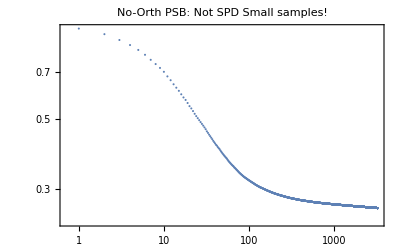

```mathematica
{n,b}={125,3};
{A,H0}=RandomReal[{-1,1},{2,n,n}]; 
{A,H0}={ A+Aᵀ,H0+H0ᵀ};
InvA=Inverse[A];
MaxIter=3267;
{Hs,Hb,Hd,Hp}={H0,H0,H0,H0};
InvA=Inverse[A];
U= U0=Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
V=A.U0;
U2 = Orthogonalize[(V-U0.U0ᵀ.V)ᵀ]ᵀ;
Data=Table[
V=A.U;
Hp = PSB[Hp,{U,V}];
UNew = Orthogonalize[ RandomReal[{-1,1},{2b,n}]]ᵀ;
(*Print[Norm[Uᵀ.UNew]];*)
U=UNew;
Norm[Hp-InvA,"Frobenius"],
{MaxIter}]/Norm[H0-InvA,"Frobenius"];
ListLogLogPlot[Data,
GridLines->Automatic,
PlotRange->All,
PlotLabel->"No-Orth PSB: Not SPD Small samples!",
Frame->True]
```